# Practical 6

Solution of Cauchy problem for first order partial differential order

Q1.SOLVE the PDE xu_x+yu_y=u+1

```mathematica
Eqn1:=x*D[u[x,y],x]+y*D[u[x,y],y]==u[x,y]+1;
```

```mathematica
Sol=DSolve[Eqn1,u[x,y],{x,y}]
```

{{u[x,y]→-1+x C[1][y/x]}}

```mathematica
{{u[x,y]->-1+x C[1][y/x]}}(*general solution*)
```

```mathematica
Par=u[x,y]/.Sol/.C[1][y/x]->1
```

```mathematica
{-1+x}(*particular solution*)
```

```mathematica
Plot3D[Par,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}]
```

```mathematica
Parl=u[x,y]/.Sol/.C[1][y/x]->y/x
```

{-1+y}

```mathematica
Plot3D[Parl,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}]
```

Question 2:Solve the pde 3 u_x+2 u_y=0

```mathematica
Eqn2:=3D[u[x,y],x]+2*D[u[x,y],y]==0;
```

```mathematica
Sol=DSolve[Eqn2,u[x,y],{x,y}]
```

{{u[x,y]→C[1][1/3 (-2 x+3 y)]}}

```mathematica
{{u[x,y]->C[1][1/3 (-2 x+3 y)]}}(*General solution*)
Par1=u[x,y]/.Sol/.C[1][1/3*(-2*x+3*y)]->1
```

{{u[x,y]→C[1][1/3 (-2 x+3 y)]}}

```mathematica
{1}(*Particular solution*)
```

```mathematica
Plot3D[Par1,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}]
```

Q3.Solve the PDE 3 u_x+2 u_y=0 given  u[x,0]=Sin[x]

```mathematica
Eqn3:=3*D[u[x,y],x]+2*D[u[x,y],y]==0;
```

```mathematica
Sol3=DSolve[{Eqn3,u[x,0]==Sin[x]},u[x,y],{x,y}]
```

{{u[x,y]→Sin[1/2 (2 x-3 y)]}}

```mathematica
p1=Plot3D[u[x,y]/.Sol3,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p3=ParametricPlot3D[{x,0,Sin[x]},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p3]
```

Observation-above graph shows the particular solution of the  given PDE

```mathematica
Soln1=DSolve[3*y'[x]-2==0,y[x],x](*Characteristic Equation*)
```

{{y[x]→(2 x)/3+C[1]}}

```mathematica
Par=y[x]/.Soln1/.C[1]->{-2,-1,0,1,2}
```

{{-2+(2 x)/3,-1+(2 x)/3,(2 x)/3,1+(2 x)/3,2+(2 x)/3}}

```mathematica
Plot[Par,{x,-5,5},AxesLabel->{x,y}]
```

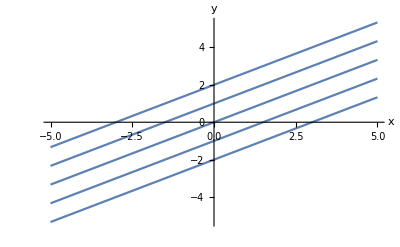

Observation-characteristics are family of Parallel Straight lines

Q4.Solve the PDE  xu_x+yu_y==u+1 with initial conditions u (x,x^2)=x^2

```mathematica
Eqn4:=x*D[u[x,y],x]+y*D[u[x,y],y]==u[x,y]+1;
```

```mathematica
Sol4=DSolve[{Eqn4,u[x,x^2]==x^2},u[x,y],{x,y}]
```

{{u[x,y]→(x^2-y+y^2)/y}}

```mathematica
p1=Plot3D[u[x,y]/.Sol4,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{x,x^2,x^2},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
p3=ParametricPlot3D[{x,x^2,2},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p2,p3]
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln2=DSolve[x*y'[x]-y[x]==0,y[x],x](*Characteristic Equation*)
```

{{y[x]→x C[1]}}

```mathematica
Par1=y[x]/.Soln2/.C[1]->{-2,-1,0,1,2}
```

{{-2 x,-x,0,x,2 x}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

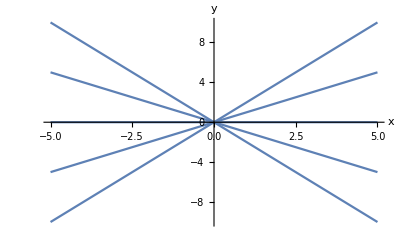

Observation-Characteristics are straight lines passing through the origin

Q5. Solve the PDE 3 Subscript[u, x]+2 u_y==0, with initial condition u (x,0)=sin[x]

```mathematica
Eqn5:=3*D[u[x,y],x]+2*D[u[x,y],y]==0;
```

```mathematica
Sol5=DSolve[{Eqn5,u[x,0]==Sin[x]},u[x,y],{x,y}]
```

{{u[x,y]→Sin[1/2 (2 x-3 y)]}}

```mathematica
{{u[x,y]->Sin[1/2 (2 x-3 y)]}}(*Particular solution*)
```

```mathematica
p1=Plot3D[u,[x,y]/.Sol5,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{x,0,Sin[x]},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln5=DSolve[3*y'[x]-2==0,y[x],x](*Characteristic Equation*)
```

{{y[x]→(2 x)/3+C[1]}}

```mathematica
Part1=y[x]/.Soln5/.C[1]->{-2,-1,0,1,2}
```

{{-2+(2 x)/3,-1+(2 x)/3,(2 x)/3,1+(2 x)/3,2+(2 x)/3}}

```mathematica
Plot[Part1,{x,-5,5},AxesLabel->{x,y}]
```

Observation-Characteristics are family of Parallel Straight lines

Q6:Solve the PDE yu_x+ xu_y = 0 with given initial condition u[0,y]=e^-y^2

```mathematica
Eqn6:=y*D[u[x,y],x]+x*D[u[x,y],y]==0;
```

```mathematica
Sol6=DSolve[{Eqn6,u[0,y]==Exp[-y^2]},u[x,y],{x,y}]
```

{{u[x,y]→ⅇ^(x^2-y^2)}}

```mathematica
p1=Plot3D[u[x,y]/.Sol6,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{0,y,Exp[-y^2]},{y,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln6=DSolve[y[x]*y'[x]-x==0,y[x],x](*Characteristic Equation*)
```

{{y[x]→-√(x^2+2 C[1])},{y[x]→√(x^2+2 C[1])}}

```mathematica
Par1=y[x]/.Soln6/.C[1]->{-2,-1,0,1,2}
```

{{-√(-4+x^2),-√(-2+x^2),-√(x^2),-√(2+x^2),-√(4+x^2)},{√(-4+x^2),√(-2+x^2),√(x^2),√(2+x^2),√(4+x^2)}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

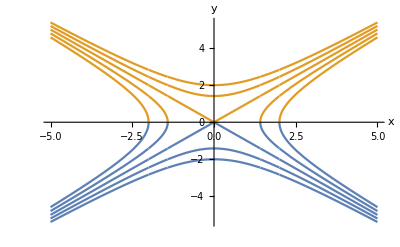

Observation - Characteristics are Hyperbolic curves wit two straight lines passing through origin and asymptotic to hyperbolic curves.

Q7:Solve  the PDE xu_x+ yu_y = xy, with given initial condition u[x,x^2]=2

```mathematica
Eqn7:=x*D[u[x,y],x]+y*D[u[x,y],y]==x*y;
```

```mathematica
Sol7=DSolve[{Eqn7,u[x,x^2]==2},u[x,y],{x,y}]
```

{{u[x,y]→(4 x^3+x^4 y-y^3)/(2 x^3)}}

```mathematica
{{u[x,y]->(4 x^3+x^4 y-y^3)/(2 x^3)}}(*Particular solution*)
```

```mathematica
p1=Plot3D[u[x,y]/.Sol7,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{x,x^2,2},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln7=DSolve[x*y'[x]-y[x]==0,y[x],x](*Characteristic Equation*)
```

{{y[x]→x C[1]}}

```mathematica
Par1=y[x]/.Soln7/.C[1]->{-2,-1,0,1,2}
```

{{-2 x,-x,0,x,2 x}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

Observation - Characteristics are Straight lines passing through the origin

Q8:Solve the PDE Subscript[u, x]+xu_y==0, with given initial condition u[0,y]=Sin[y]

```mathematica
Eqn8:=D[u[x,y],x]+x*D[u[x,y],y]==0;
```

```mathematica
Sol8=DSolve[{Eqn8,u[0,y]==Sin[y]},u[x,y],{x,y}]
```

{{u[x,y]→Sin[1/2 (-x^2+2 y)]}}

```mathematica
p1=Plot3D[u[x,y]/.Sol8,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{0,y,Sin[y]},{Y,-5,5},PlotStyle->{Red ,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln8=DSolve[y'[x]==x,y[x],x](*Characteristic Euation*)
```

{{y[x]→x^2/2+C[1]}}

```mathematica
Par1=y[x]/.Soln8/.C[1]->{-2,-1,0,1,2}
```

{{-2+x^2/2,-1+x^2/2,x^2/2,1+x^2/2,2+x^2/2}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

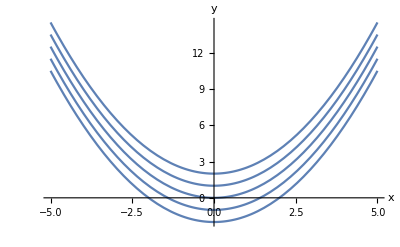

Observation - Characteristics are family of Parabolic Curves

Q9: Solve the PDE u_x+ xu_y = (y-((x^2)/2))^2, with the given initial condition u[0,y] = e^y

```mathematica
Eqn9:=1*D[u[x,y],x]+x*D[u[x,y],y]==(y-((x^2)/2))^2;
```

```mathematica
Sol9=DSolve[{Eqn9,u[0,y]==Exp[y]},u[x,y],{x,y}]
```

```mathematica
{{u[x,y]->1/4 ⅇ^(-x^2/2) (4 ⅇ^y+ⅇ^(x^2/2) x^5-4 ⅇ^(x^2/2) x^3 y+4 ⅇ^(x^2/2) x y^2)}}(*Particular solution*)
```

```mathematica
p1=Plot3D[u[x,y]/.Sol9,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{0,y,Sin[y]},{y,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln9=DSolve[y'[x]==x,y[x],x](*Characteristic Equation*)
```

{{y[x]→x^2/2+C[1]}}

```mathematica
Par1=y[x]/.Soln9/.C[1]->{-2,-1,0,1,2}
```

{{-2+x^2/2,-1+x^2/2,x^2/2,1+x^2/2,2+x^2/2}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

Observation - Characteristics are family of Parabolic Curves
Q10.Solve the PDE u_x + xu_y =y, with the initial condition u[1,y]=2y

```mathematica
Eqn10:=1*D[u[x,y],x]+x*D[u[x,y],y]==y;
```

```mathematica
Sol10=DSolve[{Eqn10,u[1,y]==2*y},u[x,y],{x,y}]
```

```mathematica
{{u[x,y]->1/6 (5-3 x^2-2 x^3+6 y+6 x y)}}(*Particular Solution*)
```

```mathematica
p1=Plot3D[u[x,y]/.Sol10,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{1,y,2*y},{y,-5,5},PlotStyle->{Red ,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln10=DSolve[y'[x]==x,y[x],x](*Characteristics equation*)
```

{{y[x]→x^2/2+C[1]}}

```mathematica
Par1=y[x]/.Soln10/.C[1]->{-2,-1,0,1,2}
```

{{-2+x^2/2,-1+x^2/2,x^2/2,1+x^2/2,2+x^2/2}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

Observation - Characteristics are family of Parabolic curves
Q10. Solve the PDE u_x + xu_y = y , with given initial condition u[0,y]=y^2

```mathematica
Eqn11:=1*D[u[x,y],x]+x*D[u[x,y],y]==y;
```

```mathematica
Sol11=DSolve[{Eqn11,u[0,y]==y^2},u[x,y],{x,y}]
```

{{u[x,y]→1/12 (-4 x^3+3 x^4+12 x y-12 x^2 y+12 y^2)}}

```mathematica
p1=Plot3D[u[x,y]/.Sol11,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{0,y,y^2},{y,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln11=DSolve[y'[x]==x,y[x],x](*Characteristic Equation*)
```

{{y[x]→x^2/2+C[1]}}

```mathematica
Par1=y[x]/.Soln11/.C[1]->{-2,-1,0,1,2}
```

{{-2+x^2/2,-1+x^2/2,x^2/2,1+x^2/2,2+x^2/2}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```

Observation - Characteristics are family of Parabolic curves
Q12. Solve the PDE Subscript[xu, x]+(x+y)u_y=u+1 , with given initial condition [x,0]=x^2

```mathematica
Eqn12:=x*D[u[x,y],x]+(x+y)*D[u[x,y],y]==u[x,y]+1;
```

```mathematica
Sol12=DSolve[{Eqn12,u[x,0]==x^2},u[x,y],{x,y}]
```

{{u[x,y]→ⅇ^(-y/x) (-ⅇ^(y/x)+ⅇ^((2 y)/x)+x^2)}}

```mathematica
p1=Plot3D[u[x,y]/.Sol12,{x,-5,5},{y,-5,5},AxesLabel->{x,y,u}];
```

```mathematica
p2=ParametricPlot3D[{x,0,x^2},{x,-5,5},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
Show[p1,p2]
```

```mathematica
Soln12=DSolve[y'[x]==1+(y[x]/x),y[x],x](*Characteristics Equation*)
```

{{y[x]→x C[1]+x Log[x]}}

```mathematica
Par1=y[x]/.Soln12/.C[1]->{-2,-1,0,1,2}
```

{{-2 x+x Log[x],-x+x Log[x],x Log[x],x+x Log[x],2 x+x Log[x]}}

```mathematica
Plot[Par1,{x,-5,5},AxesLabel->{x,y}]
```